```mathematica
Hold[FullForm[{1 , 2 , 3}]]
```

Hold[List[1,2,3]]

```mathematica
Table[elementMojejTabelki[i],{i , 1 , 10}]
```

{elementMojejTabelki[1],elementMojejTabelki[2],elementMojejTabelki[3],elementMojejTabelki[4],elementMojejTabelki[5],elementMojejTabelki[6],elementMojejTabelki[7],elementMojejTabelki[8],elementMojejTabelki[9],elementMojejTabelki[10]}

```mathematica
FullForm[Table[elementMojejTabelki[i],{i , 1 , 10}]]
```

List[elementMojejTabelki[1],elementMojejTabelki[2],elementMojejTabelki[3],elementMojejTabelki[4],elementMojejTabelki[5],elementMojejTabelki[6],elementMojejTabelki[7],elementMojejTabelki[8],elementMojejTabelki[9],elementMojejTabelki[10]]

```mathematica
{1 , 2 , 3 , 4}[[1]]
```

1

```mathematica
Hold[FullForm[{1 , 2 , 3 , 4}[[1]]]]
```

Hold[Part[List[1,2,3,4],1]]

```mathematica
{1 , 2 , 3 , 4}[[-1]]
```

4

```mathematica
{1 , 2 , 3 , 4}[[-2]]
```

3

```mathematica
{1 , 2 , 3 , 4}[[2;;3]]
```

{2,3}

```mathematica
Hold[FullForm[{1 , 2 , 3 , 4}[[2;;3]]]]
```

Hold[Part[List[1,2,3,4],Span[2,3]]]

```mathematica
{1 , 2 , 3 , 4}[[-2;;]]
```

{3,4}

```mathematica
{1 , 2 , 3 , 4}[[;;-2]]
```

{1,2,3}

```mathematica
Hold[FullForm[{1 , 2 , 3 , 4}[[-2;;]]]]
```

Hold[Part[List[1,2,3,4],Span[-2,All]]]

```mathematica
Hold[FullForm[{1 , 2 , 3 , 4}[[-2;;-1]]]]
```

Hold[Part[List[1,2,3,4],Span[-2,-1]]]

```mathematica
mojaDwuWymiarowaTabelka=Table[el[row , col] , {row , 1 , 3} , {col , 1 , 4}];
```

```mathematica
TableForm[mojaDwuWymiarowaTabelka , TableHeadings->{{"pierwszy rząd" , "drugi rząd" , "trzeci rząd"},{"pierwsza kolumna" , "druga kolumna" , "trzecia kolumna" , "czwarta kolumna"}}]
```

| pierwsza kolumna | druga kolumna | trzecia kolumna | czwarta kolumna
pierwszy rząd | el[1,1] | el[1,2] | el[1,3] | el[1,4]
drugi rząd | el[2,1] | el[2,2] | el[2,3] | el[2,4]
trzeci rząd | el[3,1] | el[3,2] | el[3,3] | el[3,4]

```mathematica
MatrixForm[mojaDwuWymiarowaTabelka]
```

(el[1,1] | el[1,2] | el[1,3] | el[1,4]
el[2,1] | el[2,2] | el[2,3] | el[2,4]
el[3,1] | el[3,2] | el[3,3] | el[3,4])

```mathematica
{1 , 2}
```

```mathematica
{3 , 4}
```

```mathematica
Join[{1 , 2} , {3 , 4}]
```

{1,2,3,4}

```mathematica
Join[{{1 , 11} , {2 , 22}} , {{3 , 33} , {4,44}}]
```

{{1,11},{2,22},{3,33},{4,44}}

```mathematica
{1 , 2 , 3 , 4}[[0]]
```

List

```mathematica
FullForm[{1 , 2 , 3 , 4}]
```

List[1,2,3,4]

```mathematica
Head[{1 , 2 , 3 , 4}]
```

List

```mathematica
?Append
```

```mathematica
Append[{1 , 2 , 3} , 4]
```

{1,2,3,4}

```mathematica
?AppendTo
```

```mathematica
krótkaLista = {1 , 2 , 3 , 4};
```

```mathematica
Print[krótkaLista]
```

{1,2,3,4}

```mathematica
AppendTo[krótkaLista , 5]
```

{1,2,3,4,5}

```mathematica
Print[krótkaLista]
```

{1,2,3,4,5}

```mathematica
Partition[{1 , 2 , 3 , 4 , 5 , 6},2]
```

{{1,2},{3,4},{5,6}}

```mathematica
%//TableForm
```

1 | 2
3 | 4
5 | 6

```mathematica
Hold[FullForm[f[x]]]
```

Hold[f[x]]

```mathematica
Hold[FullForm[x//f]]
```

Hold[f[x]]

```mathematica
Riffle[{4 , 3 , 1 , 2},{5 , 8 , 6 , 7}]
```

{4,5,3,8,1,6,2,7}

```mathematica
Partition[Riffle[{4 , 3 , 1 , 2},{5 , 8 , 6 , 7}] , 2]
```

{{4,5},{3,8},{1,6},{2,7}}

```mathematica
f/@{1 , 2 , 3 , 4}
```

{f[1],f[2],f[3],f[4]}

```mathematica
Hold[FullForm[f/@{1 , 2 , 3 , 4}]]
```

Hold[Map[f,List[1,2,3,4]]]

```mathematica
(*f*)
```

```mathematica
(*{1 , 2 , 3 , 4}*)
```

```mathematica
(*{f[1] , f[2] , f[3] , f[4]}*)
```

```mathematica
f[x_]:=Point[x];
```

```mathematica
myPointData = Partition[Riffle[{4 , 3 , 1 , 2},{5 , 8 , 6 , 7}] , 2]
```

{{4,5},{3,8},{1,6},{2,7}}

```mathematica
g/@myPointData
```

{g[{4,5}],g[{3,8}],g[{1,6}],g[{2,7}]}

```mathematica
f/@myPointData
```

{Point[{4,5}],Point[{3,8}],Point[{1,6}],Point[{2,7}]}

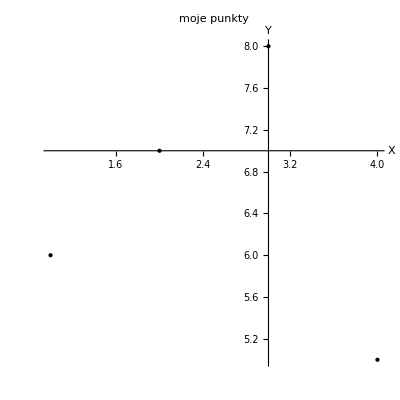

```mathematica
Graphics[f/@myPointData , Axes->True , PlotRange->All , AxesOrigin->{3 , 7} , AxesLabel->{"X" , "Y"} , PlotLabel->"moje punkty"]
```

```mathematica
(*ESC + pi + ESC*)
```

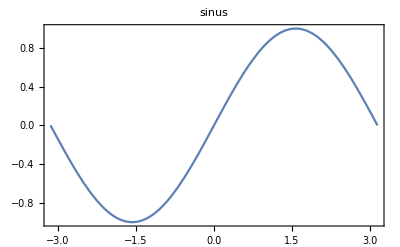

```mathematica
Plot[Sin[x] , {x , -π , π} , Axes->False ,Frame->True, PlotLabel->"sinus"]
```

```mathematica
Plot[Sin[x] , {x , -π , π} , Axes->False ,Frame->True, PlotLabel->"sinus"]//FullForm
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[-3.14159,-1.28228×10^-7],List[-3.13967,-0.00192716],List[-3.13774,-0.00385419],List[-3.13388,-0.0077082],List[-3.12618,-0.0154158],List[-3.11076,-0.0308278],List[-3.07993,-0.0616262],List[-3.01826,-0.123018],List[-2.88456,-0.254214],List[-2.75971,-0.372665],List[-2.63732,-0.483172],List[-2.50455,-0.594821],List[-2.38064,-0.68961],List[-2.24636,-0.780355],List[-2.2443,-0.781642],List[-2.24224,-0.782925],List[-2.23812,-0.785481],List[-2.22988,-0.790554],List[-2.2134,-0.800538],List[-2.18044,-0.819851],List[-2.11453,-0.855785],List[-2.1126,-0.856778],List[-2.11068,-0.857767],List[-2.10684,-0.859736],List[-2.09915,-0.863636],List[-2.08378,-0.871283],List[-2.05304,-0.885957],List[-2.05112,-0.886846],List[-2.0492,-0.887733],List[-2.04535,-0.889495],List[-2.03767,-0.892981],List[-2.0223,-0.899794],List[-1.99155,-0.91278],List[-1.98947,-0.913629],List[-1.98739,-0.914474],List[-1.98322,-0.916153],List[-1.97488,-0.919461],List[-1.95822,-0.925887],List[-1.92488,-0.937965],List[-1.9228,-0.938685],List[-1.92071,-0.939402],List[-1.91655,-0.940822],List[-1.90821,-0.943614],List[-1.89154,-0.949],List[-1.85821,-0.958981],List[-1.85626,-0.959531],List[-1.85432,-0.960077],List[-1.85043,-0.961158],List[-1.84264,-0.963276],List[-1.82708,-0.967338],List[-1.82514,-0.967829],List[-1.82319,-0.968316],List[-1.8193,-0.969281],List[-1.81152,-0.971165],List[-1.79596,-0.974757],List[-1.79402,-0.975189],List[-1.79207,-0.975618],List[-1.78818,-0.976465],List[-1.7804,-0.978113],List[-1.76484,-0.981232],List[-1.7629,-0.981606],List[-1.76095,-0.981975],List[-1.75706,-0.982703],List[-1.74928,-0.984114],List[-1.73372,-0.986757],List[-1.73181,-0.987065],List[-1.72991,-0.987369],List[-1.72609,-0.987966],List[-1.71846,-0.989117],List[-1.71656,-0.989396],List[-1.71465,-0.989671],List[-1.71084,-0.99021],List[-1.70321,-0.991246],List[-1.7013,-0.991496],List[-1.6994,-0.991742],List[-1.69558,-0.992224],List[-1.68795,-0.993145],List[-1.6727,-0.994812],List[-1.67079,-0.995004],List[-1.66889,-0.995193],List[-1.66507,-0.995559],List[-1.65745,-0.996248],List[-1.65554,-0.996412],List[-1.65363,-0.996571],List[-1.64982,-0.996879],List[-1.64219,-0.997452],List[-1.64028,-0.997587],List[-1.63838,-0.997717],List[-1.63456,-0.997968],List[-1.63266,-0.998087],List[-1.63075,-0.998203],List[-1.62694,-0.998425],List[-1.62503,-0.99853],List[-1.62312,-0.998631],List[-1.61931,-0.998824],List[-1.6174,-0.998914],List[-1.6155,-0.999001],List[-1.61168,-0.999164],List[-1.60961,-0.999247],List[-1.60754,-0.999325],List[-1.60547,-0.999399],List[-1.60341,-0.999468],List[-1.60134,-0.999534],List[-1.59927,-0.999595],List[-1.59513,-0.999704],List[-1.59306,-0.999752],List[-1.59099,-0.999796],List[-1.58892,-0.999836],List[-1.58685,-0.999871],List[-1.58479,-0.999902],List[-1.58272,-0.999929],List[-1.58065,-0.999951],List[-1.57858,-0.99997],List[-1.57651,-0.999984],List[-1.57444,-0.999993],List[-1.57237,-0.999999],List[-1.5703,-1.],List[-1.56823,-0.999997],List[-1.56616,-0.999989],List[-1.5641,-0.999978],List[-1.56203,-0.999962],List[-1.55996,-0.999941],List[-1.55789,-0.999917],List[-1.55582,-0.999888],List[-1.55375,-0.999855],List[-1.55168,-0.999817],List[-1.54961,-0.999776],List[-1.54754,-0.99973],List[-1.54548,-0.999679],List[-1.54341,-0.999625],List[-1.54134,-0.999566],List[-1.53927,-0.999503],List[-1.5372,-0.999436],List[-1.53513,-0.999364],List[-1.53306,-0.999288],List[-1.52892,-0.999123],List[-1.52686,-0.999035],List[-1.52479,-0.998942],List[-1.52065,-0.998743],List[-1.51237,-0.998294],List[-1.5103,-0.998171],List[-1.50823,-0.998044],List[-1.5041,-0.997776],List[-1.49582,-0.997191],List[-1.49375,-0.997034],List[-1.49168,-0.996872],List[-1.48755,-0.996537],List[-1.47927,-0.995814],List[-1.47734,-0.995636],List[-1.47541,-0.995454],List[-1.47155,-0.995079],List[-1.46383,-0.994284],List[-1.4619,-0.994076],List[-1.45996,-0.993864],List[-1.4561,-0.99343],List[-1.44838,-0.992517],List[-1.44645,-0.992279],List[-1.44452,-0.992038],List[-1.44066,-0.991544],List[-1.43294,-0.990513],List[-1.41749,-0.988272],List[-1.41556,-0.987976],List[-1.41363,-0.987675],List[-1.40977,-0.987064],List[-1.40205,-0.985796],List[-1.38661,-0.983085],List[-1.35572,-0.97696],List[-1.35363,-0.976511],List[-1.35153,-0.976058],List[-1.34735,-0.975139],List[-1.33898,-0.97325],List[-1.32224,-0.969268],List[-1.28876,-0.96049],List[-1.28666,-0.959905],List[-1.28457,-0.959316],List[-1.28039,-0.958126],List[-1.27202,-0.955696],List[-1.25527,-0.950635],List[-1.22179,-0.939714],List[-1.21974,-0.93901],List[-1.21768,-0.938301],List[-1.21358,-0.936873],List[-1.20536,-0.933968],List[-1.18892,-0.927969],List[-1.15606,-0.915221],List[-1.09032,-0.886774],List[-1.0884,-0.885887],List[-1.08649,-0.884996],List[-1.08265,-0.883206],List[-1.07499,-0.879586],List[-1.05966,-0.872191],List[-1.02901,-0.856789],List[-0.967702,-0.823584],List[-0.965624,-0.822404],List[-0.963546,-0.82122],List[-0.95939,-0.818841],List[-0.951078,-0.814042],List[-0.934454,-0.804275],List[-0.901207,-0.784076],List[-0.834712,-0.741103],List[-0.710583,-0.652275],List[-0.576079,-0.54474],List[-0.444025,-0.429578],List[-0.320831,-0.315355],List[-0.187263,-0.186171],List[-0.062556,-0.0625152],List[0.0597025,0.0596671],List[0.192335,0.191151],List[0.316107,0.310869],List[0.450253,0.435193],List[0.58195,0.549654],List[0.704786,0.647871],List[0.837997,0.743305],List[0.83994,0.744603],List[0.841883,0.745899],List[0.845769,0.748481],List[0.853541,0.753613],List[0.869085,0.763738],List[0.900172,0.783434],List[0.962347,0.820535],List[0.964252,0.821623],List[0.966157,0.822707],List[0.969966,0.824866],List[0.977585,0.82915],List[0.992822,0.837571],List[1.0233,0.853829],List[1.0252,0.854819],List[1.02711,0.855806],List[1.03092,0.85777],List[1.03854,0.861662],List[1.05377,0.869294],List[1.08425,0.883952],List[1.08632,0.884917],List[1.08838,0.885877],List[1.09252,0.887787],List[1.10078,0.891562],List[1.11732,0.898928],List[1.15039,0.912921],List[1.15245,0.913763],List[1.15452,0.914601],List[1.15865,0.916264],List[1.16692,0.919545],List[1.18345,0.925916],List[1.21652,0.937899],List[1.21845,0.938566],List[1.22038,0.93923],List[1.22424,0.940547],List[1.23195,0.943139],List[1.24738,0.948154],List[1.27823,0.957507],List[1.28016,0.958061],List[1.28209,0.958612],List[1.28594,0.959703],List[1.29366,0.961842],List[1.30908,0.965948],List[1.33994,0.97347],List[1.34203,0.973947],List[1.34412,0.974419],List[1.3483,0.97535],List[1.35666,0.977161],List[1.37339,0.980578],List[1.37548,0.980986],List[1.37757,0.981389],List[1.38175,0.982183],List[1.39011,0.98372],List[1.40683,0.986588],List[1.40892,0.986927],List[1.41101,0.987262],List[1.41519,0.987918],List[1.42356,0.98918],List[1.42565,0.989484],List[1.42774,0.989784],List[1.43192,0.990372],List[1.44028,0.991495],List[1.44237,0.991765],List[1.44446,0.99203],List[1.44864,0.992548],List[1.457,0.993533],List[1.47373,0.995292],List[1.47568,0.99548],List[1.47763,0.995663],List[1.48153,0.996019],List[1.48934,0.996684],List[1.49129,0.996841],List[1.49325,0.996995],List[1.49715,0.997289],List[1.50496,0.997833],List[1.50691,0.99796],List[1.50886,0.998083],List[1.51277,0.998317],List[1.51472,0.998428],List[1.51667,0.998536],List[1.52057,0.998739],List[1.52253,0.998835],List[1.52448,0.998928],List[1.52838,0.999101],List[1.53033,0.999182],List[1.53229,0.999259],List[1.53619,0.999401],List[1.53814,0.999467],List[1.54009,0.999529],List[1.54205,0.999587],List[1.544,0.999641],List[1.54595,0.999691],List[1.5479,0.999738],List[1.54985,0.999781],List[1.55181,0.99982],List[1.55376,0.999855],List[1.55571,0.999886],List[1.55766,0.999914],List[1.55961,0.999937],List[1.56157,0.999957],List[1.56352,0.999974],List[1.56547,0.999986],List[1.56742,0.999994],List[1.56937,0.999999],List[1.57133,1.],List[1.57328,0.999997],List[1.57523,0.99999],List[1.57718,0.99998],List[1.57913,0.999965],List[1.58109,0.999947],List[1.58304,0.999925],List[1.58499,0.999899],List[1.58694,0.99987],List[1.58889,0.999836],List[1.59085,0.999799],List[1.5928,0.999758],List[1.59475,0.999713],List[1.59866,0.999612],List[1.60057,0.999557],List[1.60248,0.999498],List[1.60631,0.999369],List[1.60822,0.9993],List[1.61014,0.999226],List[1.61396,0.999068],List[1.61588,0.998984],List[1.61779,0.998896],List[1.62162,0.998709],List[1.62927,0.998291],List[1.63119,0.998177],List[1.6331,0.99806],List[1.63693,0.997814],List[1.64458,0.997279],List[1.6465,0.997136],List[1.64841,0.996989],List[1.65224,0.996685],List[1.65989,0.996033],List[1.66181,0.995861],List[1.66372,0.995686],List[1.66755,0.995323],List[1.6752,0.994554],List[1.67712,0.994353],List[1.67903,0.994148],List[1.68286,0.993727],List[1.69051,0.992842],List[1.69243,0.992612],List[1.69434,0.992378],List[1.69817,0.991899],List[1.70582,0.990898],List[1.72113,0.988721],List[1.72321,0.988407],List[1.72529,0.98809],List[1.72944,0.987443],List[1.73774,0.986097],List[1.75435,0.983202],List[1.75642,0.982821],List[1.7585,0.982435],List[1.76265,0.981652],List[1.77095,0.980035],List[1.78756,0.976598],List[1.78964,0.97615],List[1.79171,0.975697],List[1.79586,0.974779],List[1.80417,0.972892],List[1.82077,0.968918],List[1.85399,0.960169],List[1.85592,0.959625],List[1.85786,0.959079],List[1.86174,0.957974],List[1.86949,0.955723],List[1.88499,0.951047],List[1.91598,0.941012],List[1.91792,0.940355],List[1.91986,0.939694],List[1.92373,0.938362],List[1.93148,0.935655],List[1.94698,0.930073],List[1.97798,0.91824],List[1.98008,0.917406],List[1.98218,0.916569],List[1.98638,0.914882],List[1.99478,0.911459],List[2.01157,0.904421],List[2.04516,0.889582],List[2.11235,0.85691],List[2.11441,0.855846],List[2.11647,0.854778],List[2.12059,0.852631],List[2.12884,0.848294],List[2.14533,0.839448],List[2.17831,0.821072],List[2.24426,0.781663],List[2.36732,0.699195],List[2.50075,0.597868],List[2.62532,0.493638],List[2.74745,0.38402],List[2.87994,0.258675],List[3.00358,0.137577],List[3.00573,0.13544],List[3.00789,0.133304],List[3.0122,0.129028],List[3.02083,0.120469],List[3.03808,0.103326],List[3.07259,0.0689526],List[3.07474,0.0668011],List[3.0769,0.0646493],List[3.08121,0.0603447],List[3.08984,0.0517324],List[3.10709,0.0344969],List[3.10925,0.0323416],List[3.1114,0.0301862],List[3.11571,0.0258749],List[3.12434,0.0172511],List[3.1265,0.0150949],List[3.12865,0.0129386],List[3.13297,0.00862592],List[3.13512,0.00646951],List[3.13728,0.00431306],List[3.13944,0.0021566],List[3.14159,1.28228×10^-7]]]],"Charting`Private`Tag$11356#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[False,False]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[True,True],List[True,True]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotLabel,"sinus"],Rule[PlotRange,List[List[Times[-1,Pi],Pi],List[-1.,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

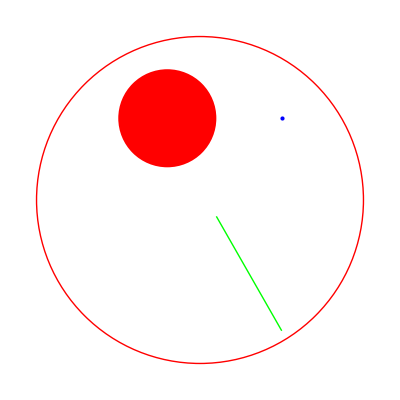

```mathematica
Graphics[
{
{
Red , 
Circle[{0,0} , 1] , 
{
Blue , 
Point[{0.5 , 0.5}]
},
Disk[{-0.2 , 0.5} , 0.3]
} , 
{
Thick , 
Green , 
Line[{{0.1 , -0.1} , {0.5 , -0.8}}]
}
}
]
```